```mathematica
f[x_]:=Piecewise[{{1+Cos[π*x], Abs[x]≤1},{0, Abs[x]>1}}]
```

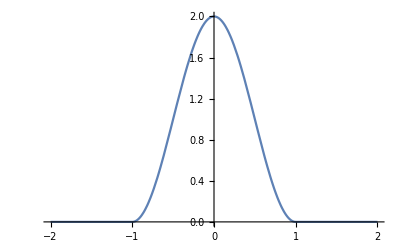

```mathematica
Plot[f[x], {x, -2,2}]
```

Transformada de senos y cosenos

```mathematica
g[w_]:=√(2/π)∫_(-∞)^∞ (f[x]Cos[w*x])ⅆx
```

```mathematica
m[w_]:=√(2/π)∫_(-∞)^∞ (f[x]Sin[w*x])ⅆx
```

```mathematica
ff=1/(√(2*π))∫_0^20 (g[w]Cos[w*x]+m[w]Sin[w*x])ⅆw
```

1/(2 π)(-CosIntegral[-(-20+π) (-1+x)] Sin[π x]+CosIntegral[-(20+π) (-1+x)] Sin[π x]+CosIntegral[(-20+π) (1+x)] Sin[π x]-CosIntegral[(20+π) (1+x)] Sin[π x]-Log[-1-x] Sin[π x]-Log[1-x] Sin[π x]+Log[-1+x] Sin[π x]+Log[1+x] Sin[π x]+2 SinIntegral[20-20 x]+Cos[π x] SinIntegral[(-20+π) (-1+x)]+2 SinIntegral[20 (1+x)]-Cos[π x] SinIntegral[(-20+π) (1+x)]+Cos[π x] SinIntegral[(20+π) (1+x)]+Cos[π x] SinIntegral[20+π-20 x-π x])

transformada compleja

```mathematica
f1[w_]:= 1/(√(2*π))∫_(-∞)^∞ f[x]*ⅇ^(-ⅈ*w*x)ⅆx
```

```mathematica
f2= 1/(√(2*π))∫_-20^20 f1[w]*ⅇ^(ⅈ*w*x)ⅆw
```

1/(8 π)ⅈ ⅇ^(-ⅈ π x) (4 ⅇ^(ⅈ π x) CosIntegral[π (-1+x)]+4 ⅇ^(ⅈ π x) CosIntegral[-π (1+x)]-4 ⅇ^(ⅈ π x) CosIntegral[π-π x]-4 ⅇ^(ⅈ π x) CosIntegral[π+π x]-4 ⅇ^(ⅈ π x) ExpIntegralEi[-20 ⅈ (-1+x)]+4 ⅇ^(ⅈ π x) ExpIntegralEi[20 ⅈ (-1+x)]+2 ⅇ^(2 ⅈ π x) ExpIntegralEi[-ⅈ (-20+π) (-1+x)]-2 ExpIntegralEi[ⅈ (-20+π) (-1+x)]-2 ⅇ^(2 ⅈ π x) ExpIntegralEi[-ⅈ (20+π) (-1+x)]+2 ExpIntegralEi[ⅈ (20+π) (-1+x)]+4 ⅇ^(ⅈ π x) ExpIntegralEi[-20 ⅈ (1+x)]-4 ⅇ^(ⅈ π x) ExpIntegralEi[20 ⅈ (1+x)]-2 ⅇ^(2 ⅈ π x) ExpIntegralEi[-ⅈ (-20+π) (1+x)]+2 ExpIntegralEi[ⅈ (-20+π) (1+x)]+2 ⅇ^(2 ⅈ π x) ExpIntegralEi[-ⅈ (20+π) (1+x)]-2 ExpIntegralEi[ⅈ (20+π) (1+x)]-4 ⅇ^(ⅈ π x) Log[π]-4 ⅇ^(ⅈ π x) Log[-1-x]+Log[-ⅈ/(-1+x)]+2 ⅇ^(ⅈ π x) Log[-ⅈ/(-1+x)]+ⅇ^(2 ⅈ π x) Log[-ⅈ/(-1+x)]-Log[ⅈ/(-1+x)]-2 ⅇ^(ⅈ π x) Log[ⅈ/(-1+x)]-ⅇ^(2 ⅈ π x) Log[ⅈ/(-1+x)]+Log[-ⅈ (-1+x)]+2 ⅇ^(ⅈ π x) Log[-ⅈ (-1+x)]+ⅇ^(2 ⅈ π x) Log[-ⅈ (-1+x)]-Log[ⅈ (-1+x)]-2 ⅇ^(ⅈ π x) Log[ⅈ (-1+x)]-ⅇ^(2 ⅈ π x) Log[ⅈ (-1+x)]-4 ⅇ^(ⅈ π x) Log[-1+x]-Log[-ⅈ/(1+x)]-2 ⅇ^(ⅈ π x) Log[-ⅈ/(1+x)]-ⅇ^(2 ⅈ π x) Log[-ⅈ/(1+x)]+Log[ⅈ/(1+x)]+2 ⅇ^(ⅈ π x) Log[ⅈ/(1+x)]+ⅇ^(2 ⅈ π x) Log[ⅈ/(1+x)]-Log[-ⅈ (1+x)]-2 ⅇ^(ⅈ π x) Log[-ⅈ (1+x)]-ⅇ^(2 ⅈ π x) Log[-ⅈ (1+x)]+Log[ⅈ (1+x)]+2 ⅇ^(ⅈ π x) Log[ⅈ (1+x)]+ⅇ^(2 ⅈ π x) Log[ⅈ (1+x)]+4 ⅇ^(ⅈ π x) Log[1+x]+4 ⅇ^(ⅈ π x) Log[π-π x])

Power::infy: Infinite expression 1/0. encountered.

General::stop: Further output of Power::infy will be suppressed during this calculation.

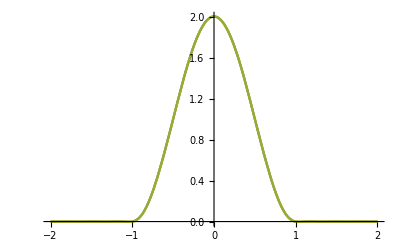

```mathematica
Plot[{ff, f[x], Re[f2]},{x, -2, 2}]
```

ahora su derivada

```mathematica
fPrim[x_]:=f'[x]
```

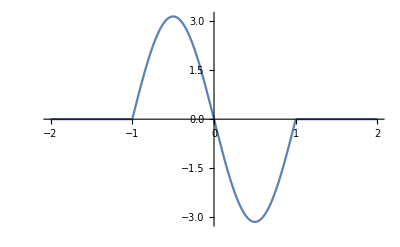

```mathematica
Plot[fPrim[x],{x,-2,2}]
```

transformada de senos y cosenos para la derivada de f

```mathematica
g[w_]:=√(2/π)∫_(-∞)^∞ (fPrim[x]Cos[w*x])ⅆx
```

```mathematica
m[w_]:=√(2/π)∫_(-∞)^∞ (fPrim[x]Sin[w*x])ⅆx
```

```mathematica
ff2=1/(√(2*π))∫_0^20 (g[w]Cos[w*x]+m[w]Sin[w*x])ⅆw
```

1/2 (-Cos[π x] CosIntegral[-(-20+π) (-1+x)]+Cos[π x] CosIntegral[-2 π (-1+x)]-Cos[π x] CosIntegral[2 π (-1+x)]+Cos[π x] CosIntegral[-(20+π) (-1+x)]+Cos[π x] CosIntegral[(-20+π) (1+x)]-Cos[π x] CosIntegral[-2 π (1+x)]+Cos[π x] CosIntegral[2 π (1+x)]-Cos[π x] CosIntegral[(20+π) (1+x)]-2 Cos[π x] Log[1-x]+2 Cos[π x] Log[-1+x]+Sin[π x] SinIntegral[(20-π) (-1+x)]+Sin[π x] SinIntegral[(-20+π) (1+x)]-Sin[π x] SinIntegral[(20+π) (1+x)]-Sin[π x] SinIntegral[20+π-20 x-π x])

transformada compleja para la derivada de f

```mathematica
f1[w_]:= 1/(√(2*π))∫_(-∞)^∞ fPrim[x]*ⅇ^(-ⅈ*w*x)ⅆx
```

```mathematica
f2= 1/(√(2*π))∫_-20^20 f1[w]*ⅇ^(ⅈ*w*x)ⅆw
```

1/8 ⅇ^(-ⅈ π x) (-2 ⅇ^(2 ⅈ π x) ExpIntegralEi[-ⅈ (-20+π) (-1+x)]-2 ExpIntegralEi[ⅈ (-20+π) (-1+x)]+2 ⅇ^(2 ⅈ π x) ExpIntegralEi[-ⅈ (20+π) (-1+x)]+2 ExpIntegralEi[ⅈ (20+π) (-1+x)]+2 ⅇ^(2 ⅈ π x) ExpIntegralEi[-ⅈ (-20+π) (1+x)]+2 ExpIntegralEi[ⅈ (-20+π) (1+x)]-2 ⅇ^(2 ⅈ π x) ExpIntegralEi[-ⅈ (20+π) (1+x)]-2 ExpIntegralEi[ⅈ (20+π) (1+x)]+Log[-ⅈ/(-1+x)]-ⅇ^(2 ⅈ π x) Log[-ⅈ/(-1+x)]-Log[ⅈ/(-1+x)]+ⅇ^(2 ⅈ π x) Log[ⅈ/(-1+x)]+Log[-ⅈ (-1+x)]-ⅇ^(2 ⅈ π x) Log[-ⅈ (-1+x)]-Log[ⅈ (-1+x)]+ⅇ^(2 ⅈ π x) Log[ⅈ (-1+x)]-Log[-ⅈ/(1+x)]+ⅇ^(2 ⅈ π x) Log[-ⅈ/(1+x)]+Log[ⅈ/(1+x)]-ⅇ^(2 ⅈ π x) Log[ⅈ/(1+x)]-Log[-ⅈ (1+x)]+ⅇ^(2 ⅈ π x) Log[-ⅈ (1+x)]+Log[ⅈ (1+x)]-ⅇ^(2 ⅈ π x) Log[ⅈ (1+x)])

Power::infy: Infinite expression 1/0. encountered.

General::stop: Further output of Power::infy will be suppressed during this calculation.

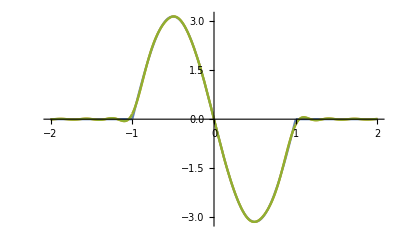

```mathematica
Plot[{fPrim[x], ff2, Re[f2]},{x,-2,2}]
```

## Ahora el B del primer punto

```mathematica
y[x_]:=ⅇ^(-3*Abs[x])*Sin[2*x]
```

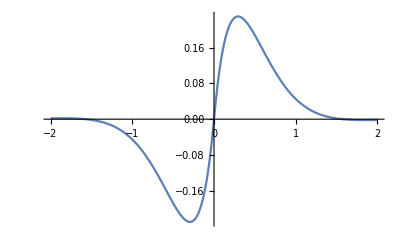

```mathematica
Plot[y[x], {x, -2,2}]
```

```mathematica
y'[x]
```

2 ⅇ^(-3 Abs[x]) Cos[2 x]-3 ⅇ^(-3 Abs[x]) Sin[2 x] Abs'[x]

```mathematica
g[w_]:=√(2/π)∫_∞^∞ (y[x]Cos[w*x])ⅆx
```

```mathematica
m[w_]:=√(2/π)∫_(∞□)^∞ (y[x]Sin[w*x])ⅆx
```

```mathematica
ff=1/(√(2*π))∫_0^20 (g[w]Cos[w*x]+m[w]Sin[w*x])ⅆw
```

ConditionalExpression[0,Re[□]>0&&Im[□]==0&&(□∉Reals||□ ∞∉Reals)]

transformada compleja

```mathematica
f1[w_]:= 1/(√(2*π))∫_(-∞)^∞ y[x]*ⅇ^(-ⅈ*w*x)ⅆx
```

```mathematica
f2= 1/(√(2*π))∫_-20^20 f1[w]*ⅇ^(ⅈ*w*x)ⅆw
```

ConditionalExpression[-1/(2 π)ⅈ (CosIntegral[(-18+3 ⅈ) x] Sin[(2+3 ⅈ) x]-CosIntegral[(22+3 ⅈ) x] Sin[(2+3 ⅈ) x]-ⅈ (CosIntegral[(-22+3 ⅈ) x] Sinh[(3+2 ⅈ) x]-CosIntegral[(-18-3 ⅈ) x] Sinh[(3+2 ⅈ) x]+CosIntegral[(-2+3 ⅈ) x] Sinh[(3+2 ⅈ) x]-CosIntegral[(2-3 ⅈ) x] Sinh[(3+2 ⅈ) x]-Log[(-22+3 ⅈ) x] Sinh[(3+2 ⅈ) x]-Log[(-2+3 ⅈ) x] Sinh[(3+2 ⅈ) x]+Log[(2-3 ⅈ) x] Sinh[(3+2 ⅈ) x]+Log[(22-3 ⅈ) x] Sinh[(3+2 ⅈ) x]+ⅈ Cosh[(3+2 ⅈ) x] SinIntegral[(-22+3 ⅈ) x]-ⅈ Cos[(2+3 ⅈ) x] SinIntegral[(-18+3 ⅈ) x]-ⅈ Cosh[(3+2 ⅈ) x] SinIntegral[(18+3 ⅈ) x]+ⅈ Cos[(2+3 ⅈ) x] SinIntegral[(22+3 ⅈ) x])),(Im[x]<0&&(3 Re[x]≤2 Im[x]||Re[x]≥-6 Im[x]))||(Im[x]>0&&(Re[x]≤-(2 Im[x])/3||Re[x]≥6 Im[x]))]

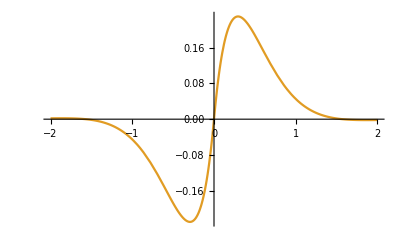

```mathematica
Plot[{ff, y[x], Re[f2]},{x,-2,2}]
```

para la derivada de y

```mathematica
yPrima[x_]:=y'[x]
```

```mathematica
Plot[yPrima[x], {x,-1,1}]
```

-Graphics-

```mathematica
g[w_]:=√(2/π)∫_∞^∞ (yPrima[x]Cos[w*x])ⅆx
```

```mathematica
m[w_]:=√(2/π)∫_(∞□)^∞ (yPrima[x]Sin[w*x])ⅆx
```

```mathematica
ff2=1/(√(2*π))∫_0^20 (g[w]Cos[w*x]+m[w]Sin[w*x])ⅆw
```

$Aborted

## Segundo punto

```mathematica
a[w_]:=√(2*π)*ⅇ^(-2*Abs[w])
```

```mathematica
ax=1/(√(2*π))∫_-20^20 a[w]*ⅇ^(ⅈ*w*x)ⅆw
```

(ⅇ^(-40-20 ⅈ x) (-2+4 ⅇ^(40+20 ⅈ x)-2 ⅇ^(40 ⅈ x)+ⅈ x-ⅈ ⅇ^(40 ⅈ x) x))/((-2 ⅈ+x) (2 ⅈ+x))

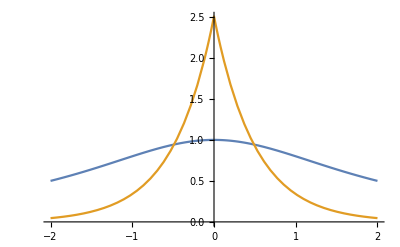

```mathematica
Plot[{ax, a[x]},{x,-2,2}]
```

```mathematica
b[w_]:=Cos[4*w+π/3]
```

```mathematica
bx=1/(√(2*π))∫_-20^20 b[w]*ⅇ^(ⅈ*w*x)ⅆw
```

(ⅇ^(-20 ⅈ x) (4 Cos[80+π/6]+ⅇ^(40 ⅈ x) (-4 Cos[80-π/6]+ⅈ x Sin[80-π/6])+ⅈ x Sin[80+π/6]))/(√(2 π) (-16+x^2))

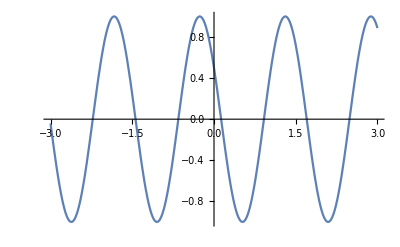

```mathematica
Plot[{b[x]},{x,-3,3}]
```

```mathematica
c[w_]:=(2*Sin[3*(w*2*π)])/(w-2*π)
```

```mathematica
cx=1/(√(2*π))∫_(-∞)^∞ c[w]*ⅇ^(ⅈ*w*x)ⅆw
```

Integrate::idiv: Integral of (2 ⅇ^(ⅈ w x) Sin[6 π w])/(-2 π+w) does not converge on {-∞,∞}.

(∫_(-∞)^∞ (2 ⅇ^(ⅈ w x) Sin[6 π w])/(-2 π+w)ⅆw)/(√(2 π))

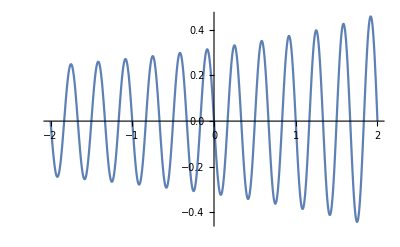

```mathematica
Plot[c[x],{x,-2,2}]
```

```mathematica
d[w_]:=Piecewise[{{-1, -3≤w≤-2},{w+1,-2<w<-1 },{0, -1≤ w≤1},{w-1,1<w≤ 2 },{1, 2<w<3}}]
```

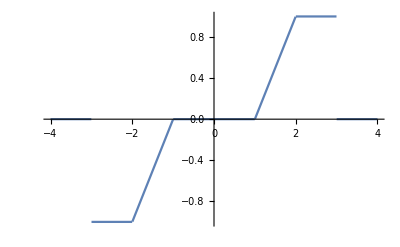

```mathematica
Plot[d[w], {w,-4,4}]
```

```mathematica
dx=1/(√(2*π))∫_-20^20 d[w]*ⅇ^(ⅈ*w*x)ⅆw
```

(ⅇ^(-3 ⅈ x) (-ⅇ^(ⅈ x)+ⅇ^(2 ⅈ x)-ⅇ^(4 ⅈ x)+ⅇ^(5 ⅈ x)-ⅈ x-ⅈ ⅇ^(6 ⅈ x) x))/(√(2 π) x^2)